### Chernoff Faces Jones Lin and Grant Ovsepyan

A Chernoff face is a simple sketch of a human face that is parameterized by a few variables. By manipulating the variables, it is possible to achieve a wide range of expressions. Here are a few auxiliary functions (evaluate these before running the Manipulate) below.

```mathematica
face=Circle[{0,0},{1,1.2}];pupNow={0,0};left=1;right=2;
eyeRadius=0.18;eyeCenter={{-0.4,0.15},{0.4,0.15}};pupilRadius=0.09;
browUp=0.25;browW=0.2;browAng=Pi/20;
eye[side_,eccen_]:={Black,Circle[eyeCenter[[side]],{eyeRadius+0.05,eyeRadius+eccen}]};
pupil[side_,pup_,eccen_]:={Disk[eyeCenter[[side]]+pup+{0,pup[[2]] eccen},pupilRadius+Max[0,eccen/3]],Black,Disk[eyeCenter[[side]]+pup+{0,pup[[2]] eccen},0.03]};
browDraw[side_,{browAng_,browLift_},eccen_]:=Rotate[{Thickness[0.01],Line[{{eyeCenter[[side]]+{-browW,browLift+browUp+0.5 eccen},eyeCenter[[side]]+{browW,browLift+browUp+0.5 eccen}}}]},2 (side-1.5) browAng];
mouthDraw[s_]:=ParametricPlot[{Cos[u],-s Sin[u]},{u,Pi/6,Pi-Pi/6},Axes->False,PlotStyle->{Red,Thickness[0.02]},PlotRange->All];
```

Now you can create many expressive faces by moving the sliders and grabbing the eyes with the mouse. See if you can make it happy. Sad? Angry?

```mathematica
Manipulate[eyeMat={{1/(eyeRadius-pupilRadius/2),0},{0,1/(0.15+eyes-pupilRadius/2)}};
If[Norm[eyeMat.(pup-eyeCenter[[left]])]<1,pupNow=pup-eyeCenter[[left]];];
If[Norm[eyeMat.(pup-eyeCenter[[right]])]<1,pupNow=pup-eyeCenter[[right]];];
Graphics[{face,eye[left,eyes],eye[right,eyes],Blue,pupil[left,pupNow,eyes],pupil[right,pupNow,eyes],Black,browDraw[left,brows,eyes],browDraw[right,brows,eyes],Inset[mouthDraw[mouth],{0,-0.5}]},ImageSize->{400,450}],{{brows,{-Pi/20,0}},{-0.6,0},{0.6,0.15},ControlPlacement->Left},{{eyes,0},-0.07,0.07,ControlPlacement->Left,ControlType->VerticalSlider},{{mouth,0.15},-0.401,0.4,0.01,ControlPlacement->Left,ControlType->VerticalSlider},{{pup,{0,0}},Locator,Appearance->None},SaveDefinitions->True]
```

I originally wrote this in answer to a StackExchange question:

```mathematica
URL["https://mathematica.stackexchange.com/questions/143988/how-to-define-a-function-to-produce-a-chernoff-face"]
```

URL[https://mathematica.stackexchange.com/questions/143988/how-to-define-a-function-to-produce-a-chernoff-face]

### Chernoff Photos #1

Your goal in this part of the project is to start with a full-face photo, and to create a Manipulate that will cause the photo to undergo expression changes analogous to the simple line drawing above. So if your friend in the photo is smiling, you can grab the mouth slider and make them sad. If their eyebrows are curved gently down, you can make them angry by moving the brows slider. If the eyes are narrow, you can widen them with the eye slider to make them look surprised.

In order to accomplish this task, you will need to locate facial features. Fortunately, there is a command called

```mathematica
?FacialFeatures
```

that does a pretty reasonable job. You will want to study the help file for this function. The parent function FeatureExtract may also be useful (though it may not be needed, depending on how you proceed). Of course, you will also want to use some of the spatial mapping functions like those in the Spatial Mappings section of the Visual Vocabulary.

Start with some of the photos from actors and characters from Game of Thrones. Then do the same kind of thing for (at east) 3 other photo images of faces. Perhaps a self-portrait would be fitting.

For this project, you should pass in your function (a Manipulate somewhat similar to the above) along with several examples of how it works on photos of different faces. Show that you can make the faces change expressions. Good luck and have fun!

```mathematica
gamePeople=-Graphics-;
```

By googling around, you can find an alternative implementation of Chernoff faces:

```mathematica
URL["https://mathematicaforprediction.wordpress.com/2016/06/03/making-chernoff-faces-for-data-visualization/"]
```

URL[https://mathematicaforprediction.wordpress.com/2016/06/03/making-chernoff-faces-for-data-visualization/]

This link also has a nice writeup about how to use Chernoff faces for data visualization. Feel free to use this or other accessible resources if they are helpful.

```mathematica
a = 4;sigma=0.7;mu=1.0;gau[x_]:=x^2;
```

```mathematica
chernoffFace[image_]:= Module[{},
(*The code creates a grid of points for interpolating facial features,with a grid size of 100. The grid is a two-dimensional array of points,with the x-coordinate ranging from 0 to 1 and the y-coordinate ranging from 0 to 1. The grid is created using the Flatten and Table functions,which are used to generate a list of points with the desired x and y coordinates.Once the grid is created,it can be used to modify the facial features of an image.For example,the manipulateEyes and manipulateMouth functions can be applied to the grid to alter the features of the eyes and mouth.The grid can then be interpolated to create a smooth,continuous representation of the modified facial features.This can be used to create a wide range of facial expressions in an image.*)
gridSize=40;
grid=Flatten[Table[{i,j},{i,0,1,1/(gridSize-1)},{j,0,1,1/(gridSize-1)}],1];




(*The manipulateMouth function is a tool for modifying the features of the mouth in a face.It takes as input a grid representing the face,as well as the indices of the points that make up the mouth in the grid.The function first calculates the mean position of all mouth points,then uses the square of the distance between each point and the mean position to determine the direction in which the mouth should be altered.The strength parameter determines the degree of alteration.The function uses a for loop to iterate over the points that make up the mouth,and calculates the square of the distance between each point and the mean position of the mouth.It then updates the y-coordinate of each point by adding a strengthd version of the squared distance to the y-coordinate.This results in the desired alteration of the mouth,creating either a smile or a frown.*)
(*To use the manipulateMouth function,simply provide it with a grid representing the face,the indices of the points that make up the mouth in the grid,and a strength factor to determine the degree of alteration.The function will return a modified grid with the modified mouth features.*)
manipulateMouth[grid_,mouthIndex_,strength_]:=Module[{},targetGrid=grid;
For[i=1,i≤Length[mouthIndex],i++,
diff = targetGrid[[mouthIndex[[i]]]][[1]]-Mean[targetGrid[[mouthIndex]]][[1]];
diff = gau[Abs[diff]];
targetGrid[[mouthIndex[[i]]]][[2]]+=strength*diff;];
targetGrid];

(*Function to change eyebrow features in a face*)
(*This function alters the eyebrow points by first calculating mean position for both left and right eyebrow points.
Then based on strength value, it increases/decreases the y coordinates of eyebrow points based on whether an
eyebrow point is left/right of the mean position for each eyebrow. Amount of change is relative to difference
between x-coordinates of mean eyebrow point and the eyebrow point. *)
(*To use the manipulateMouth function,simply provide it with a grid representing the face,the indices of the points that make up the mouth in the grid,and a strength factor to determine the degree of alteration.The function will return a modified grid with the modified mouth features.*)
manipulateEyeBrows[grid_,leftEyeBrowIndex_,rightEyeBrowIndex_,strength_]:=Module[{},targetGrid=grid;
temp=strength;
For[i=1,i≤Length[leftEyeBrowIndex],i++,If[i≤Length[leftEyeBrowIndex]/2,temp=strength,temp=-1 strength];
diff = targetGrid[[leftEyeBrowIndex[[i]]]][[1]]-Mean[targetGrid[[leftEyeBrowIndex]]][[1]];
diff =Sign[diff]* gau[Abs[diff]];
targetGrid[[leftEyeBrowIndex[[i]]]][[2]]+=temp*(diff);];
temp=strength;
For[i=1,i≤Length[rightEyeBrowIndex],i++,If[i≤Length[rightEyeBrowIndex]/2,temp=strength,temp=-1 strength];
diff = targetGrid[[rightEyeBrowIndex[[i]]]][[1]]-Mean[targetGrid[[rightEyeBrowIndex]]][[1]];
diff =Sign[diff]* gau[Abs[diff]];
targetGrid[[rightEyeBrowIndex[[i]]]][[2]]+=temp*(diff);];
targetGrid];

(*The manipulateEyes function is a tool for modifying the features of the eyes in a face.It takes as input a grid representing the face,as well as the indices of the left and right eyes in the grid.The function first calculates the mean position of each eye,then uses the distance between each point in the eye and the mean position to determine the direction in which the eye should be enlarged or diminished.The strength parameter determines the degree of enlargement or diminishment.The function uses a for loop to iterate over the points in each eye,and calculates the distance between each point and the mean position of the eye.It then updates the coordinates of each point by adding a strengthd version of the distance to the x and y coordinates.This results in the desired enlargement or diminishment of the eye.*)
manipulateEyes[grid_,IndexOfLeftEye_,IndexOfRightEye_,strength_]:=Module[{},targetGrid=grid;
leftEyeCenter=Mean[targetGrid[[IndexOfLeftEye]]];
For[i=1,i<=Length[IndexOfLeftEye],i++,distance=targetGrid[[IndexOfLeftEye[[i]]]]-leftEyeCenter;
distance=Sign[distance]*gau[Abs[distance]];
targetGrid[[IndexOfLeftEye[[i]]]][[1]]+=strength*distance[[1]];
targetGrid[[IndexOfLeftEye[[i]]]][[2]]+=strength*distance[[2]];];
rightEyeCenter=Mean[targetGrid[[IndexOfRightEye]]];
For[i=1,i<=Length[IndexOfRightEye],i++,distance=targetGrid[[IndexOfRightEye[[i]]]]-rightEyeCenter;
distance=Sign[distance]*gau[Abs[distance]];
targetGrid[[IndexOfRightEye[[i]]]][[1]]+=strength*distance[[1]];
targetGrid[[IndexOfRightEye[[i]]]][[2]]+=strength*distance[[2]];];
targetGrid];

(*The code is used to find the normalized coordinates of the left and right eye features in an image,as well as the corresponding nearest points in the interpolation grid.It does this by using the FacialFeatures function to extract the coordinates of the left and right eye features in the image.These coordinates are then normalized by dividing them by the dimensions of the image.Next,the Nearest function is used to find the indices of the nearest points in the interpolation grid for each of the left and right eye points.These indices are stored in the nearestLeftEyePointsIndex and nearestRightEyePointsIndex variables,respectively.These indices can then be used to modify the corresponding points in the interpolation grid using the manipulateEyes function.This will result in a modified grid with altered eye features,which can be interpolated to create a smooth,continuous representation of the modified eyes.*)
w = ImageDimensions[image][[1]];h = ImageDimensions[image][[2]];
leftEyePoints=FacialFeatures[image,"LeftEyePoints"][[1]];
leftEyePoints[[All,1]]/=w;
leftEyePoints[[All,2]]/=h;

rightEyePoints=FacialFeatures[image,"RightEyePoints"][[1]];
rightEyePoints[[All,1]]/=w;
rightEyePoints[[All,2]]/=h;

nearestLeftEyePointsIndex=Nearest[grid->"Index",leftEyePoints];
nearestRightEyePointsIndex=Nearest[grid->"Index",rightEyePoints];


(*This code first extracts the dimensions of the image using the ImageDimensions function,and stores them in the imageDimensions variable.It then uses the FacialFeatures function to extract the coordinates of the mouth features in the image,and divides these coordinates by the image dimensions to normalize them.These normalized coordinates are stored in the mouthCoordinates variable.Finally,the Nearest function is used to find the indices of the nearest points in the interpolation grid for each of the mouth points.These indices are stored in the nearestMouthIndices variable.These indices can then be used to modify the corresponding points in the interpolation grid using the manipulateMouth function.This will result in a modified grid with altered mouth features,which can be interpolated to create a smooth,continuous representation of the modified face.*)
mouthPoints=FacialFeatures[image,"MouthExternalPoints"][[1]];
mouthPoints[[All,1]]/=w;
mouthPoints[[All,2]]/=h;
nearestMouthPointsIndex=Nearest[grid->"Index",mouthPoints];


(*The code is a part of a larger program that finds the normalized coordinates of the left and right eyebrow features in an image.It then uses these coordinates to find the corresponding nearest points in an interpolation grid created earlier in the program.The code first uses the FacialFeatures function to extract the coordinates of the left and right eyebrow points in the image.It then normalizes these coordinates by dividing each coordinate by the width and height of the image,respectively.Next,the code uses the Nearest function to find the indices of the nearest points in the interpolation grid for the left and right eyebrow points.The Nearest function takes two arguments:the interpolation grid and the eyebrow points.It uses the "Index" method to return the indices of the nearest points in the grid.The resulting indices are stored in the nearestLeftEyeBrowPointsIndex and nearestRightEyeBrowPointsIndex variables.*)
leftEyeBrowPoints=FacialFeatures[image,"LeftEyebrowPoints"][[1]];
rightEyeBrowPoints=FacialFeatures[image,"RightEyebrowPoints"][[1]];
leftEyeBrowPoints[[All,1]]/=w;
leftEyeBrowPoints[[All,2]]/=h;
rightEyeBrowPoints[[All,1]]/=w;
rightEyeBrowPoints[[All,2]]/=h;
nearestLeftEyeBrowPointsIndex=Nearest[grid->"Index",leftEyeBrowPoints];
nearestRightEyeBrowPointsIndex=Nearest[grid->"Index",rightEyeBrowPoints];

(*The function begins by defining a colorFunction using BSplineFunction and ImageData,which is used to color the image.Next,the code defines several functions to manipulate the positions of the face features (mouth,eyes,and eyebrows) using the manipulateMouth,manipulateEyes,and manipulateEyeBrows functions.The code then creates an interpolation function using the updated grid of points and plots the image using ParametricPlot.The PlotPoints option is controlled by the active state of a control,allowing the user to adjust the level of detail in the plotted image.Overall,this function allows the user to interactively manipulate the positions of the mouth,eyes,and eyebrows on an image using Manipulate and ParametricPlot.*)
Manipulate[

gau[x_]:=augmentionStrength*x;Module[{},colorFunction=BSplineFunction[ImageData[image],SplineDegree->1];
(*If the position of the mouth slider is altered,update the interpolation grid.*)
intermediateGrid=manipulateMouth[grid,Flatten[nearestMouthPointsIndex],mouth];

(*If the position of the eyes slider is modified,update the interpolation grid.*)
intermediateGrid=manipulateEyes[intermediateGrid,Flatten[nearestLeftEyePointsIndex],Flatten[nearestRightEyePointsIndex],eyes];

(*If the position of the eyebrows slider is altered,update the interpolation grid.*)
intermediateGrid=manipulateEyeBrows[intermediateGrid,Flatten[nearestLeftEyeBrowPointsIndex],Flatten[nearestRightEyeBrowPointsIndex],brows];

(*Construct an interpolation function based on the updated grid,and use it to generate a plot of the image using the ParametricPlot[] function. *)
f=Interpolation[Flatten[Table[{{N[1/(gridSize-1)]i ,N[1/(gridSize-1)]j},intermediateGrid[[gridSize  i+j+1]]},{i,0,gridSize-1},{j,0,gridSize-1}],1],Method->"Hermite",InterpolationOrder->1];
ParametricPlot[f[u,v],{u,0,1},{v,0,1},ColorFunction->(colorFunction[1-#4,#3]&),MaxRecursion->0,PlotPoints->ControlActive[20,200],Mesh->None,ImageSize->300,PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[.03],FrameTicks->None,AspectRatio->ImageAspectRatio[image]]],

(*Slider controls that allow users to adjust various facial features.*)
{{augmentionStrength,0.5},0.0,1.0,ControlPlacement->Right,ControlType->VerticalSlider},
{{brows,0},-0.5,0.5,ControlPlacement->Right,ControlType->VerticalSlider},
{{eyes,0},-0.5,0.5,ControlPlacement->Left,ControlType->VerticalSlider},
{{mouth,0},-0.5,0.5,ControlPlacement->Left,ControlType->VerticalSlider}]
]
```

-Graphics-

```mathematica
img=-Graphics-;
chernoffFace[img]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[nearestMouthPointsIndex].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[nearestLeftEyePointsIndex].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[nearestRightEyePointsIndex].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

Table::iterb: Iterator {i,0,-1+gridSize} does not have appropriate bounds.

Interpolation::innd: First argument in Table[{{N[1/Plus[«2»]] i,N[1/Plus[«2»]] j},intermediateGrid⟦gridSize i+j+1⟧},{i,0,-1+gridSize},{j,0,gridSize-1}] does not contain a list of data and coordinates.

Table::iterb: Iterator {i,0.,-1.+gridSize} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Interpolation::innd: First argument in Table[{{N[1./Plus[«2»]] i,N[1./Plus[«2»]] j},intermediateGrid⟦gridSize i+j+1⟧},{i,0.,-1.+gridSize},{j,0.,gridSize-1.}] does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

### Chernoff Photos #2

In the second part of the project, you are asked to do something interesting with your Chernoff photo-faces method from Part #1. What do I mean by “interesting”? Below are some suggestions, but please feel free to think up your own. Creativity will be rewarded.

Example #1: Mathematica’s function CurrentImage[] gets an image from the computer’s camera. Use the CurrentImage[] as input to the Chernoff photo-face by making the eyes look in whatever direction things are changing the most.

```mathematica
chernoffFaceWithMusic[image_, totalStrengh_]:= Module[{},


(*The code creates a grid of points for interpolating facial features,with a grid size of 100. The grid is a two-dimensional array of points,with the x-coordinate ranging from 0 to 1 and the y-coordinate ranging from 0 to 1. The grid is created using the Flatten and Table functions,which are used to generate a list of points with the desired x and y coordinates.Once the grid is created,it can be used to modify the facial features of an image.For example,the manipulateEyes and manipulateMouth functions can be applied to the grid to alter the features of the eyes and mouth.The grid can then be interpolated to create a smooth,continuous representation of the modified facial features.This can be used to create a wide range of facial expressions in an image.*)
gridSize=30;
grid=Flatten[Table[{i,j},{i,0,1,1/(gridSize-1)},{j,0,1,1/(gridSize-1)}],1];




(*The manipulateMouth function is a tool for modifying the features of the mouth in a face.It takes as input a grid representing the face,as well as the indices of the points that make up the mouth in the grid.The function first calculates the mean position of all mouth points,then uses the square of the distance between each point and the mean position to determine the direction in which the mouth should be altered.The strength parameter determines the degree of alteration.The function uses a for loop to iterate over the points that make up the mouth,and calculates the square of the distance between each point and the mean position of the mouth.It then updates the y-coordinate of each point by adding a strengthd version of the squared distance to the y-coordinate.This results in the desired alteration of the mouth,creating either a smile or a frown.*)
(*To use the manipulateMouth function,simply provide it with a grid representing the face,the indices of the points that make up the mouth in the grid,and a strength factor to determine the degree of alteration.The function will return a modified grid with the modified mouth features.*)
manipulateMouth[grid_,mouthIndex_,strength_]:=Module[{},targetGrid=grid;
For[i=1,i≤Length[mouthIndex],i++,
diff = targetGrid[[mouthIndex[[i]]]][[1]]-Mean[targetGrid[[mouthIndex]]][[1]];
diff = gau[Abs[diff]];
targetGrid[[mouthIndex[[i]]]][[2]]+=strength*diff;];
targetGrid];

(*Function to change eyebrow features in a face*)
(*This function alters the eyebrow points by first calculating mean position for both left and right eyebrow points.
Then based on strength value, it increases/decreases the y coordinates of eyebrow points based on whether an
eyebrow point is left/right of the mean position for each eyebrow. Amount of change is relative to difference
between x-coordinates of mean eyebrow point and the eyebrow point. *)
(*To use the manipulateMouth function,simply provide it with a grid representing the face,the indices of the points that make up the mouth in the grid,and a strength factor to determine the degree of alteration.The function will return a modified grid with the modified mouth features.*)
manipulateEyeBrows[grid_,leftEyeBrowIndex_,rightEyeBrowIndex_,strength_]:=Module[{},targetGrid=grid;
temp=strength;
For[i=1,i≤Length[leftEyeBrowIndex],i++,If[i≤Length[leftEyeBrowIndex]/2,temp=strength,temp=-1 strength];
diff = targetGrid[[leftEyeBrowIndex[[i]]]][[1]]-Mean[targetGrid[[leftEyeBrowIndex]]][[1]];
diff =Sign[diff]* gau[Abs[diff]];
targetGrid[[leftEyeBrowIndex[[i]]]][[2]]+=temp*(diff);];
temp=strength;
For[i=1,i≤Length[rightEyeBrowIndex],i++,If[i≤Length[rightEyeBrowIndex]/2,temp=strength,temp=-1 strength];
diff = targetGrid[[rightEyeBrowIndex[[i]]]][[1]]-Mean[targetGrid[[rightEyeBrowIndex]]][[1]];
diff =Sign[diff]* gau[Abs[diff]];
targetGrid[[rightEyeBrowIndex[[i]]]][[2]]+=temp*(diff);];
targetGrid];



(*The manipulateEyes function is a tool for modifying the features of the eyes in a face.It takes as input a grid representing the face,as well as the indices of the left and right eyes in the grid.The function first calculates the mean position of each eye,then uses the distance between each point in the eye and the mean position to determine the direction in which the eye should be enlarged or diminished.The strength parameter determines the degree of enlargement or diminishment.The function uses a for loop to iterate over the points in each eye,and calculates the distance between each point and the mean position of the eye.It then updates the coordinates of each point by adding a strengthd version of the distance to the x and y coordinates.This results in the desired enlargement or diminishment of the eye.*)
manipulateEyes[grid_,IndexOfLeftEye_,IndexOfRightEye_,strength_]:=Module[{},targetGrid=grid;
leftEyeCenter=Mean[targetGrid[[IndexOfLeftEye]]];
For[i=1,i<=Length[IndexOfLeftEye],i++,distance=targetGrid[[IndexOfLeftEye[[i]]]]-leftEyeCenter;
distance=Sign[distance]*gau[Abs[distance]];
targetGrid[[IndexOfLeftEye[[i]]]][[1]]+=strength*distance[[1]];
targetGrid[[IndexOfLeftEye[[i]]]][[2]]+=strength*distance[[2]];];
rightEyeCenter=Mean[targetGrid[[IndexOfRightEye]]];
For[i=1,i<=Length[IndexOfRightEye],i++,distance=targetGrid[[IndexOfRightEye[[i]]]]-rightEyeCenter;
distance=Sign[distance]*gau[Abs[distance]];
targetGrid[[IndexOfRightEye[[i]]]][[1]]+=strength*distance[[1]];
targetGrid[[IndexOfRightEye[[i]]]][[2]]+=strength*distance[[2]];];
targetGrid];


(*The code is used to find the normalized coordinates of the left and right eye features in an image,as well as the corresponding nearest points in the interpolation grid.It does this by using the FacialFeatures function to extract the coordinates of the left and right eye features in the image.These coordinates are then normalized by dividing them by the dimensions of the image.Next,the Nearest function is used to find the indices of the nearest points in the interpolation grid for each of the left and right eye points.These indices are stored in the nearestLeftEyePointsIndex and nearestRightEyePointsIndex variables,respectively.These indices can then be used to modify the corresponding points in the interpolation grid using the manipulateEyes function.This will result in a modified grid with altered eye features,which can be interpolated to create a smooth,continuous representation of the modified eyes.*)
w = ImageDimensions[image][[1]];h = ImageDimensions[image][[2]];
leftEyePoints=FacialFeatures[image,"LeftEyePoints"][[1]];
leftEyePoints[[All,1]]/=w;
leftEyePoints[[All,2]]/=h;

rightEyePoints=FacialFeatures[image,"RightEyePoints"][[1]];
rightEyePoints[[All,1]]/=w;
rightEyePoints[[All,2]]/=h;

nearestLeftEyePointsIndex=Nearest[grid->"Index",leftEyePoints];
nearestRightEyePointsIndex=Nearest[grid->"Index",rightEyePoints];


(*This code first extracts the dimensions of the image using the ImageDimensions function,and stores them in the imageDimensions variable.It then uses the FacialFeatures function to extract the coordinates of the mouth features in the image,and divides these coordinates by the image dimensions to normalize them.These normalized coordinates are stored in the mouthCoordinates variable.Finally,the Nearest function is used to find the indices of the nearest points in the interpolation grid for each of the mouth points.These indices are stored in the nearestMouthIndices variable.These indices can then be used to modify the corresponding points in the interpolation grid using the manipulateMouth function.This will result in a modified grid with altered mouth features,which can be interpolated to create a smooth,continuous representation of the modified face.*)
mouthPoints=FacialFeatures[image,"MouthExternalPoints"][[1]];
mouthPoints[[All,1]]/=w;
mouthPoints[[All,2]]/=h;
nearestMouthPointsIndex=Nearest[grid->"Index",mouthPoints];


(*The code is a part of a larger program that finds the normalized coordinates of the left and right eyebrow features in an image.It then uses these coordinates to find the corresponding nearest points in an interpolation grid created earlier in the program.The code first uses the FacialFeatures function to extract the coordinates of the left and right eyebrow points in the image.It then normalizes these coordinates by dividing each coordinate by the width and height of the image,respectively.Next,the code uses the Nearest function to find the indices of the nearest points in the interpolation grid for the left and right eyebrow points.The Nearest function takes two arguments:the interpolation grid and the eyebrow points.It uses the "Index" method to return the indices of the nearest points in the grid.The resulting indices are stored in the nearestLeftEyeBrowPointsIndex and nearestRightEyeBrowPointsIndex variables.*)
leftEyeBrowPoints=FacialFeatures[image,"LeftEyebrowPoints"][[1]];
rightEyeBrowPoints=FacialFeatures[image,"RightEyebrowPoints"][[1]];
leftEyeBrowPoints[[All,1]]/=w;
leftEyeBrowPoints[[All,2]]/=h;
rightEyeBrowPoints[[All,1]]/=w;
rightEyeBrowPoints[[All,2]]/=h;
nearestLeftEyeBrowPointsIndex=Nearest[grid->"Index",leftEyeBrowPoints];
nearestRightEyeBrowPointsIndex=Nearest[grid->"Index",rightEyeBrowPoints];

(*The function begins by defining a colorFunction using BSplineFunction and ImageData,which is used to color the image.Next,the code defines several functions to manipulate the positions of the face features (mouth,eyes,and eyebrows) using the manipulateMouth,manipulateEyes,and manipulateEyeBrows functions.The code then creates an interpolation function using the updated grid of points and plots the image using ParametricPlot.The PlotPoints option is controlled by the active state of a control,allowing the user to adjust the level of detail in the plotted image.Overall,this function allows the user to interactively manipulate the positions of the mouth,eyes,and eyebrows on an image using Manipulate and ParametricPlot.*)
Manipulate[

gau[x_]:=totalStrengh*x^2;Module[{},colorFunction=BSplineFunction[ImageData[image],SplineDegree->1];
(*If the position of the mouth slider is altered,update the interpolation grid.*)
intermediateGrid=manipulateMouth[grid,Flatten[nearestMouthPointsIndex],8];

(*If the position of the eyes slider is modified,update the interpolation grid.*)
intermediateGrid=manipulateEyes[intermediateGrid,Flatten[nearestLeftEyePointsIndex],Flatten[nearestRightEyePointsIndex],9];

(*If the position of the eyebrows slider is altered,update the interpolation grid.*)
intermediateGrid=manipulateEyeBrows[intermediateGrid,Flatten[nearestLeftEyeBrowPointsIndex],Flatten[nearestRightEyeBrowPointsIndex],15];

(*Construct an interpolation function based on the updated grid,and use it to generate a plot of the image using the ParametricPlot[] function. *)
f=Interpolation[Flatten[Table[{{N[1/(gridSize-1)]i ,N[1/(gridSize-1)]j},intermediateGrid[[gridSize  i+j+1]]},{i,0,gridSize-1},{j,0,gridSize-1}],1],Method->"Hermite",InterpolationOrder->1];
ParametricPlot[f[u,v],{u,0,1},{v,0,1},ColorFunction->(colorFunction[1-#4,#3]&),MaxRecursion->0,PlotPoints->ControlActive[20,200],Mesh->None,ImageSize->300,PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[.03],FrameTicks->None,AspectRatio->ImageAspectRatio[image]]],

(*Slider controls that allow users to adjust various facial features.*)
{{augmentionStrength,0},0.0,2.0,ControlPlacement->Left,ControlType->VerticalSlider}
]
]
```

```mathematica
(*The aim of this code is to use the energy of music to control the facial augmentation.When the energy of the music is high,the strength of the augmentation will be high.Otherwise,the augmentation will be less strong.*)
(*The code extracts the energy of the music and normalizes it to a range of 0 to 1. This allows the energy of the music to be easily mapped to a range of values that can be used to control the facial augmentation.*)
music=;
energy = AudioLocalMeasurements[music, "RMSAmplitude"];
energy = (energy-Min[energy])/(Max[energy]-Min[energy]);
```

```mathematica
(*This code extracts the energy of the music and uses it to determine the strength of the facial augmentation.This allows the intensity of the augmentation to be tied to the energy of the music,creating a more dynamic and engaging visual experience.*)
list = {};
For[idx=0,idx<=100,idx=idx+1;
	filenName =FileNameJoin[{"gif",StringJoin[ToString[idx],".jpg"]}];
	image = chernoffFaceWithMusic[img, energy[idx]*2.0];
	image = image//Setting;
	image = image[[1]]//Graphics;
	(*Export[filenName,image];*)
	AppendTo[list,image];
]
```

```mathematica
Export["tmp/animation.avi",list]
```

tmp/animation.avi

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["tmp/animation.avi"]]]
```

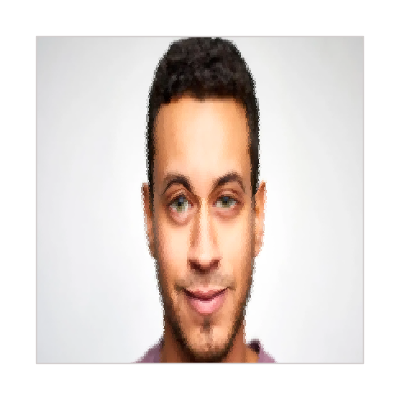
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Video["/Users/jones/tmp/animation.avi",Appearance->Automatic,AudioOutputDevice->Automatic,SoundVolume->Automatic]/Users/jones/tmp/animation.aviThumbnail1StandardForm
```